## Peak finder

```mathematica
img=Import["~/Dropbox/projects/pigun/testimgs/flp/img2.png"];
tmp=ImageData[img];
Length[tmp]
Length[tmp[[1]]]
img=ImageResize[img,{Length[tmp[[1]]]/2,Length[tmp]/2}];
img=ImageData[img];
img=0.299img[[All,All,1]]+0.587img[[All,All,2]]+0.114img[[All,All,3]];
```

720

1280

```mathematica
MatrixPlot[img,ColorFunction->GrayLevel]
```

-Graphics-

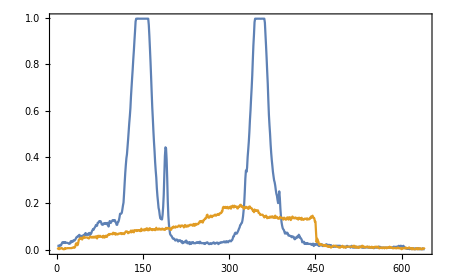

```mathematica
ListPlot[img[[{130,200}]],PlotRange->All]
```

```mathematica
ny=Length[img[[1]]];
nx=Length[img];
peaks={{-1,1,0,0,0},{-1,ny,0,0,0}};
t=0.5;

For[i=1,i≤nx,i++,(* i/x is for rows *)

status=0;
linesumx=0;
linesumy=0;

For[j=1,j≤ny,j++,(* j/y is for columns *)

If[status<0,
status++;
Continue[];
];

px=img[[i,j]];

If[px>t && status==0,(* start recording the histogram *)
status=1;
linesumy=0;linesumx=0;
];
If[px>t && status==1,(* record the histogram *)
linesumx+=px;
linesumy+=px*j;
];
If[px≤t && status==1, (* stop recording, peak ended *)
status=-5;(* enable record starting again after 5 pixels at least *)
(* store the partial result somewhere *)
total=linesumx;
(*linesumx*=i/total;
linesumy/=total;*)
thisY=linesumy/total;

(*Print[{"peak done:",i,linesumx,linesumy}];*)
(* update info in pID? *)
(* which peak is the closest in y to the *)
dists={0,0};
dists[[1]]=Abs[peaks[[1,2]]-thisY];
dists[[2]]=Abs[peaks[[2,2]]-thisY];
If[dists[[1]]<dists[[2]],pID=1;,pID=2;];(* get the closest peak *)
peaks[[pID,3]]+=total;
peaks[[pID,4]]+=linesumx*i;
peaks[[pID,5]]+=linesumy;
peaks[[pID,2]]=thisY;

];


];(* end of loop over j *)

];(* end of loop over i *)
peaks[[All,1]]=peaks[[All,4]]/peaks[[All,3]]
peaks[[All,2]]=peaks[[All,5]]/peaks[[All,3]]
peaks
```

{132.402,125.412}

{148.023,352.915}

{{132.402,148.023,1114.19,147522.,164926.},{125.412,352.915,853.761,107072.,301305.}}

```mathematica
tmp=peaks[[All,{2,1}]];
tmp={#[[1]],(360-#[[2]])}&/@tmp;
Show[{ListDensityPlot[Reverse[img]]
,ListPlot[tmp,Joined->False,PlotStyle->Red]
}]
```

-Graphics-

## Positioning

```mathematica
org={0,0,0};
h=0.1;(* distance between LED and center of bar *)
leds={org-{h,0,0},org+{h,0,0}};(* LED positions *)
p={0,-2.5,0}; (* position of the shooter *)
arm=0.6;(* length of the arm *)
armdir={0.01,1,0};armdir/=Norm[armdir];
```

```mathematica
Show[{
ListPointPlot3D[{org}, PlotStyle->Directive[{Black,PointSize[Medium]}]],
ListPointPlot3D[leds, PlotStyle->Directive[{Red,PointSize[Medium]}]],
ListPointPlot3D[{p}, PlotStyle->Directive[{Blue,PointSize[Medium]}]],
Graphics3D[{Arrow[{p,p+armdir}]}]
},PlotRange->All]
```

-Graphics3D-

## Misc Geometry

What is shown here:

1) we put the LED bar center in the origin, aligned along the x axis
2) the gun (viewpoint) sees the two LEDS at a given angle γ
3) the gun is located at some point (d,θ) in polar coordinates
3) we find the distance d that satisfies (2)

```mathematica
org={0,0,0};
h=0.1;(* distance between LED and center of bar *)
leds={org-{h,0,0},org+{h,0,0}};(* LED positions *)
```

```mathematica
p=d{Cos[θ],Sin[θ],0}; (* gun position *)
v=(#-p)&/@leds;(* vectors gun->LEDs *)
eq=v[[1]].v[[2]]/(Norm[v[[1]]]Norm[v[[2]]]);
sol=Solve[eq==Cos[γ],d];

γ0=Pi/4;

data=Table[
s=sol/.{γ->γ0,θ->t};
s=DeleteDuplicates[s];
(* filter solutions *)
s=Select[s,((γ==ArcCos[eq])/.{γ->γ0,θ->t,#[[1]]})&];
s=Select[s,#[[1,2]]>0&][[All,1,2]];
{t,s}
,{t,-Pi+Pi/90,-Pi/90,Pi/90}];
```

```mathematica
data[[1;;5]]
```

{{-(89 π)/90,{0.106227}},{-(44 π)/45,{0.112809}},{-(29 π)/30,{0.119731}},{-(43 π)/45,{0.12697}},{-(17 π)/18,{0.134502}}}

```mathematica
data1=data;
```

```mathematica
Show[{
ListPointPlot3D[{org}, PlotStyle->Directive[{Black,PointSize[Medium]}]],
ListPointPlot3D[leds, PlotStyle->Directive[{Red,PointSize[Medium]}]],
ListPointPlot3D[Table[(#{Cos[tmp[[1]]],Sin[tmp[[1]]],0}&/@tmp[[2]]),{tmp,data1}],PlotRange->All,PlotStyle->Blue],
ListPointPlot3D[Table[(#{Cos[tmp[[1]]],Sin[tmp[[1]]],0}&/@tmp[[2]]),{tmp,data}],PlotRange->All,PlotStyle->Green]
},PlotRange->All]
```

-Graphics3D-

This shows that if we are seeing the two LEDs under some angle γ, we still cannot determine both θ and d, so we cannot retrieve the gun position p.
Perhaps the relative LED intensities can tell us more.

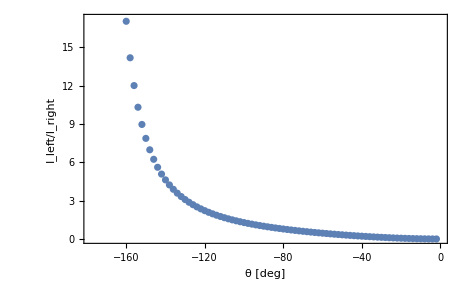

```mathematica
pts=Table[{tmp[[1]],(tmp[[2,1]]{Cos[tmp[[1]]],Sin[tmp[[1]]],0})},{tmp,data}];
(* this computes the intensity ratio: Subscript[I, left]/Subscript[I, right] *)
ListPlot[{#[[1]]180/Pi,(Norm[leds[[2]]-#[[2]]]/Norm[leds[[1]]-#[[2]]])^2}&/@pts,Frame->True,FrameLabel->{"θ [deg]","I_left/I_right"},PlotRange->Automatic]
```

Since the function is monotonic, it should be possible to uniquely determine d and θ, by knowing the angle between the two LEDs and the ratio of their intensities on the camera sensor.